## ABCD

```mathematica
<<Numbers`
```

```mathematica
free[L_]:=({{1, L}, {0, 1}})
lens[f_]:=({{1, 0}, {-1/f, 1}})
```

```mathematica
gaussianQinverse[R_,w_]:=(1/R-ⅈ λ/(π w^2))
```

```mathematica
Last@Solve[imQinv==-λ/(π w^2),w]
```

{w→(ⅈ √λ)/(√imQinv √π)}

```mathematica
inverseQprop[abcd_,qInverse_]:=(#1/#2)^-1&@@(abcd.{1/qInverse,1})
```

```mathematica
conjugate[f_]:=f/.{Complex[a_,b_]:>Complex[a,-b]}
re[f_]:=(f+(f//conjugate))/2
im[f_]:=(f-(f//conjugate))/(2ⅈ)
```

```mathematica
waist[qInverse_]:=(√λ)/(√(-(qInverse//im)) √π)
curvature[qInverse_]:=1/(qInverse//re)
```

```mathematica
inverseQprop[free[L],gaussianQinverse[∞,w0]]//Simplify//ComplexExpand
```

-(ⅈ π w0^2 λ)/(π^2 w0^4+L^2 λ^2)+(L λ^2)/(π^2 w0^4+L^2 λ^2)

```mathematica
First@Solve[zR==π w0^2/λ,λ]
```

{λ→(π w0^2)/zR}

```mathematica
(π*(π w0^2)/(π^2 w0^4+L^2 λ^2))^-1/.(First@Solve[zR==π w0^2/λ,λ])//FullSimplify
```

w0^2 (1+L^2/zR^2)

```mathematica
(inverseQprop[free[z],gaussianQinverse[∞,w0]]//waist)^2/.{λ->(π w0^2)/zR}//FullSimplify
(inverseQprop[free[z],gaussianQinverse[∞,w0]]//curvature)/.{λ->(π w0^2)/zR}//FullSimplify
```

w0^2 (1+z^2/zR^2)

z+zR^2/z

```mathematica
propagateQ[qInverse0_,elements_List]:=FoldList[inverseQprop[#2,#1]&,qInverse0,elements]
```

```mathematica
(waist[#]//FullSimplify//PowerExpand)&/@propagateQ[gaussianQinverse[∞,w0],{free[z],lens[f],free[f2]}]
```

{w0,(√(π^2 w0^4+z^2 λ^2))/(π w0),(√(π^2 w0^4+z^2 λ^2))/(π w0),(√((f-f2)^2 π^2 w0^4+(f2 z-f (f2+z))^2 λ^2))/(f π w0)}

```mathematica
freeZones[elements_]:=Cases[Thread[{Range[Length[#]],#}]&@elements,{n_,freeP[d_]}:>{n,d}]
```

```mathematica
waistPW[waists_,zones_]:=Piecewise@(
zTot=0;
{(zTot+=#2;(waists⟦#1+1⟧/.{#2->(z-(zTot-#2))})),z≤zTot}&@@@zones
)
```

```mathematica
elements={freeP[d1],lens[f],freeP[d2]};
waists=(waist[#]//FullSimplify//PowerExpand)&/@propagateQ[gaussianQinverse[∞,w0],(elements/.freeP->free)];
waistPW[waists,freeZones[elements]]
```

Piecewise[{{(√(π^2 w0^4+z^2 λ^2))/(π w0), z≤d1}, {(√(π^2 w0^4 (-d1-f+z)^2+(-f z+d1 (-d1+z))^2 λ^2))/(f π w0), z≤d1+d2}, {0, True}}]

## Example

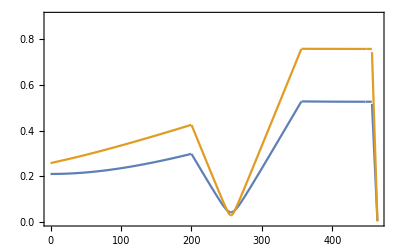

6.69373

```mathematica
elementParams={λ->698nano meters,w0->210. meters micro,L->10centi meters,d1->10centi meters,d2->10centi meters,f1->50milli meters,f2->100milli meters,δf->6milli meters,ffiber->7.93milli meters,d3->0.000001milli meters,wF->0.5*4.65 meters micro};

elements={freeP[L],freeP[d1],lens[f1],freeP[f1+f2+δf],lens[f2],freeP[d2],lens[ffiber],freeP[ffiber+d3]};
elementsRevese=Reverse@elements;
waists=(waist[#])&/@propagateQ[gaussianQinverse[∞,w0],(elements/.freeP->free)];
waistsR=(waist[#])&/@propagateQ[gaussianQinverse[∞,wF],(elementsRevese/.freeP->free)];
waistFunc=waistPW[waists,freeZones[elements]];
waistFuncR=waistPW[waistsR,freeZones[elementsRevese]];
tmp=(waistFunc/(milli meters)/.{z->Z milli meters}/.elementParams//toNumber)/.meters->1//Abs;
tmpR=(waistFuncR/(milli meters)/.{z->(zTot-Z milli meters)}/.elementParams//toNumber)/.meters->1//Abs;
Plot[{tmp,tmpR},{Z,0,(zTot/(milli meters)/.elementParams//toNumber)},PlotRange->{0,0.9},Frame->True]
1000*2*tmp/.{Z->(zTot/(milli meters)/.elementParams//toNumber)}//N
```

```mathematica
<<ABCD`
```

free::shdw: Symbol free appears in multiple contexts {ABCD`,Global`}; definitions in context ABCD` may shadow or be shadowed by other definitions.

freeP::shdw: Symbol freeP appears in multiple contexts {ABCD`,Global`}; definitions in context ABCD` may shadow or be shadowed by other definitions.

lens::shdw: Symbol lens appears in multiple contexts {ABCD`,Global`}; definitions in context ABCD` may shadow or be shadowed by other definitions.

WaistPlot::shdw: Symbol WaistPlot appears in multiple contexts {ABCD`,Global`}; definitions in context ABCD` may shadow or be shadowed by other definitions.

```mathematica
lens1loc=27.75 inches;
lens2loc=lens1loc+6.5 inches;
fiberloc=lens2loc+6 inches;
```

```mathematica
elementParams={λ->679nano meters,w0->145. meters micro,Lens1loc->lens1loc,Lens2loc->lens2loc,f2->60milli meters,Fiberloc->fiberloc, ffiber->3.68milli meters,d3->0.000001milli meters,wF->0.5*0.885milli meters};

elements={freeP[lens1loc],lens[f1],freeP[lens2loc - lens1loc],lens[f2],freeP[fiberloc-lens2loc],lens[ffiber],freeP[ffiber+d3]};
WaistPlot[tmp,{Z,0,(zTot/(milli meters)/.elementParams//toNumber)},PlotRange->{0,10.0},Frame->True]
```

WaistPlot[1000 Abs[Piecewise[{{(√(349/(10 π)))/(5000 √(ⅈ (-1/((0.-0.198487 ⅈ)+Z/1000)+1/((0.+0.198487 ⅈ)+Z/1000)))), Z/1000≤1/10||Z/1000≤1/5}, {(√(349/(10 π)))/(5000 √(ⅈ (-1/((-0.256058-0.00801681 ⅈ)+Z/1000)+1/((-0.256058+0.00801681 ⅈ)+Z/1000)))), Z/1000≤89/250}, {(√(349/(10 π)))/(5000 √(ⅈ (-1/((-0.44691-1.24731 ⅈ)+Z/1000)+1/((-0.44691+1.24731 ⅈ)+Z/1000)))), Z/1000≤57/125}, {(√(349/(10 π)))/(5000 √(ⅈ (-1/((-0.46393-0.0000504163 ⅈ)+Z/1000)+1/((-0.46393+0.0000504163 ⅈ)+Z/1000)))), Z/1000≤0.46393}, {0, True}}]],{Z,0,(1000 (d1+d2+f1+L+0.06368 meters+δf))/meters},PlotRange→{0,10.},Frame→True]

```mathematica
freeP[x]
```

freeP[x]